#### M+理论物理+ly1991提供

补集唯一法算法，速度快，但是已知对某些数独无法给出答案。

```mathematica
shudu={{5, 0, 0, 0, 0, 0, 3, 0, 0}, {0, 9, 0, 5, 0, 0, 4, 0, 0}, {0, 0, 4, 0, 0, 0, 7, 0, 0}, {0, 5, 1, 0, 3, 7, 2, 8, 9}, {3, 0, 2, 0, 8, 0, 6, 0, 4}, {0, 0, 8, 0, 5, 2, 1, 3, 7}, {0, 3, 5, 0, 0, 0, 9, 0, 0}, {6, 0, 9, 0, 0, 0, 8, 2, 3}, {0, 8, 0, 0, 2, 3, 0, 0, 6}};
```

```mathematica
l=shudu;
Grid[l,Dividers->{{Gray,Gray,Gray,Red,Gray,Gray,Red,Gray,Gray,Gray},{Gray,Gray,Gray,Red,Gray,Gray,Red,Gray,Gray,Gray}}]
```

5 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 9 | 0 | 5 | 0 | 0 | 4 | 0 | 0
0 | 0 | 4 | 0 | 0 | 0 | 7 | 0 | 0
0 | 5 | 1 | 0 | 3 | 7 | 2 | 8 | 9
3 | 0 | 2 | 0 | 8 | 0 | 6 | 0 | 4
0 | 0 | 8 | 0 | 5 | 2 | 1 | 3 | 7
0 | 3 | 5 | 0 | 0 | 0 | 9 | 0 | 0
6 | 0 | 9 | 0 | 0 | 0 | 8 | 2 | 3
0 | 8 | 0 | 0 | 2 | 3 | 0 | 0 | 6

```mathematica
Do[For[i=1,i≤9,i++,
For[j=1,j≤9,j++,
If[l[[i,j]]==0,cp=Complement[{1,2,3,4,5,6,7,8,9},l[[All,j]],l[[i,All]],Flatten[l[[3Ceiling[i/3]-2;;3Ceiling[i/3],3Ceiling[j/3]-2;;3Ceiling[j/3]]]]];If[Length[cp]==1,l[[i,j]]=First[cp]]]]],{8}]
Grid[l,Dividers->{{Gray,Gray,Gray,Red,Gray,Gray,Red,Gray,Gray,Gray},{Gray,Gray,Gray,Red,Gray,Gray,Red,Gray,Gray,Gray}}]
```

5 | 1 | 6 | 2 | 7 | 4 | 3 | 9 | 8
7 | 9 | 3 | 5 | 6 | 8 | 4 | 1 | 2
8 | 2 | 4 | 3 | 9 | 1 | 7 | 6 | 5
4 | 5 | 1 | 6 | 3 | 7 | 2 | 8 | 9
3 | 7 | 2 | 1 | 8 | 9 | 6 | 5 | 4
9 | 6 | 8 | 4 | 5 | 2 | 1 | 3 | 7
2 | 3 | 5 | 8 | 4 | 6 | 9 | 7 | 1
6 | 4 | 9 | 7 | 1 | 5 | 8 | 2 | 3
1 | 8 | 7 | 9 | 2 | 3 | 5 | 4 | 6

#### 苹果提供

枚举法，速度不稳定，运算时间从<1S到200S皆有可能，但是对任意数独皆能给出所有解

```mathematica
Clear["Global`*"]
(*对于某个数独list，第m行(或m-9列)所有空格(或者说0)处可能的填充方法*)
allprobable[list_,m_]:=Module[{a=If[m≤9,list[[m]],list[[All,m-9]]]},
ReplacePart[list,Rule@@@Transpose[{If[m≤9,{m,#},{#,m-9}]&/@Flatten@Position[a,0],#}]]&/@Permutations[Complement[Range[9],a]]];
(*将数独分为9个宫，以便后续检测是否重复*)
ninegrid[list_]:=Flatten/@Flatten[Partition[list,{3,3},3],1];
(*寻找包含0最少的行或列*)
minzero[list_]:=First@Ordering[Count[#,0]&/@Join[list,Transpose@list]/.{0->10},1];
(*检测所有行、列及9个宫是否有相同元素*)
nosameQ[list_]:=Not@MemberQ[With[{n=DeleteCases[#,0]},DeleteDuplicates[n]==n]&/@Flatten[{list,Transpose@list,ninegrid@list},1],False];
(*对包含最少的0的一行或列，填充数*)
addone[list_]:=(If[MemberQ[Flatten[#],0],Select[allprobable[#,minzero[#]],nosameQ],{#}]&/@list)~Flatten~1;
(*迭代17次必然全部填充完*)
SudokuSolve[list_]:=Nest[addone,{list},17];
```

```mathematica
data=List[List[2,0,6,0,0,1,0,8,0],List[1,7,0,0,0,9,0,6,0],List[0,0,0,4,6,7,0,0,0],List[6,1,0,0,4,0,8,0,0],List[0,0,2,0,0,0,3,0,0],List[0,0,5,0,7,0,0,9,6],List[0,0,0,2,1,5,0,0,0],List[0,3,0,6,0,0,0,2,8],List[0,2,0,7,0,0,6,0,5]];
Grid[#,Frame->All]&/@Join[{data},SudokuSolve[data]]
```

{2 | 0 | 6 | 0 | 0 | 1 | 0 | 8 | 0
1 | 7 | 0 | 0 | 0 | 9 | 0 | 6 | 0
0 | 0 | 0 | 4 | 6 | 7 | 0 | 0 | 0
6 | 1 | 0 | 0 | 4 | 0 | 8 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 5 | 0 | 7 | 0 | 0 | 9 | 6
0 | 0 | 0 | 2 | 1 | 5 | 0 | 0 | 0
0 | 3 | 0 | 6 | 0 | 0 | 0 | 2 | 8
0 | 2 | 0 | 7 | 0 | 0 | 6 | 0 | 5,2 | 9 | 6 | 3 | 5 | 1 | 7 | 8 | 4
1 | 7 | 4 | 8 | 2 | 9 | 5 | 6 | 3
8 | 5 | 3 | 4 | 6 | 7 | 2 | 1 | 9
6 | 1 | 9 | 5 | 4 | 3 | 8 | 7 | 2
7 | 4 | 2 | 9 | 8 | 6 | 3 | 5 | 1
3 | 8 | 5 | 1 | 7 | 2 | 4 | 9 | 6
4 | 6 | 8 | 2 | 1 | 5 | 9 | 3 | 7
5 | 3 | 7 | 6 | 9 | 4 | 1 | 2 | 8
9 | 2 | 1 | 7 | 3 | 8 | 6 | 4 | 5}

#### Mathematica官网提供

```mathematica
LineSimplify[data_List]:=Module[{known,d2},
			known=Cases[data,{n_}->n];
				(*Find all positions with only one possible value*)
			If[Length[Union[known]]<Length[known]||(Count[data,{}]>0),Throw[Contradiction]];
				(*If the same number is known twice, then we have a conflict*) 
				(*If there are no remaining possible values for a position then we have an error*)
			d2=Map[If[Length[#]===1,#,Complement[#,known]]&,data];
				(*Eliminate the known values from each position, except those positions that are length 1 and thus known*)
			d2/.Map[{___,#,___}->{#}&,Cases[Frequencies[Flatten[d2]],{1,n_}->n]]
				(*If a value only occurs in once place on a line then all other possibilities can be removed from that entry.*)
				(*Repeat for all numbers.*)
							];
SudokuProcess[data_]:=FixedPoint[
						Module[{workingdata=#},
							workingdata=Map[LineSimplify,workingdata];
							workingdata=Transpose[Map[LineSimplify,Transpose[workingdata]]];
							workingdata=FromSubMatrices[Map[LineSimplify,FromSubMatrices[workingdata]]]]&,
							data];
ApplySudokuLogic[data_,opts___Rule]:=Module[{firstunsolved,firstunsolvedposition,step,
											showsteps=TrueQ[ShowSteps/.{opts}/.Options[SudokuSolve]],
											(*Check for verbose message option*)
											workingdata=Catch[FixedPoint[SudokuProcess,data]]
											(*Apply the logic steps until no more progres is made*)
											},

				If[workingdata===Contradiction,Throw[Contradiction]];
				(*If a contradiction is arrived at, throw the error state up a level in the recursion*)

				If[SudokuSolvedQ[workingdata],workingdata,
					(*If the problem is solved, stop*)

					firstunsolved=First[Cases[workingdata,{n_Integer,m__Integer},{2}]];
					(*Otherwise find the first unsolved position possible values*)

					If[firstunsolved==={},Throw[Contradiction]];
					(* If there are no possible values, throw an error*)
							firstunsolvedposition=First[Position[workingdata,firstunsolved]];
					If[showsteps,Print["Guessing ",First[firstunsolved]," at ",firstunsolvedposition]];
					step=Catch[ApplySudokuLogic[ReplacePart[workingdata, Take[firstunsolved,1], firstunsolvedposition],opts]];
					(* Choose the first of the possible values and attempt to solve again*)

					If[step===Contradiction,
						If[showsteps,
							Print["Guess ",First[firstunsolved]," at ",firstunsolvedposition, " failed. Must be one of ",Rest[firstunsolved]]];
						Catch[ApplySudokuLogic[ReplacePart[workingdata, Rest[firstunsolved], firstunsolvedposition],opts]],
						(*If a contradiction results from the guess, eliminate this possibility and try to solve again*)

						step
						(*Otherwise return the result*)
						
					]
				]

			];
SudokuSolve[data_,opts___Rule]:=SudokuForm[Catch[ApplySudokuLogic[Initialize[data],opts]]];
Options[SudokuSolve]={ShowSteps->False};
SudokuSolvedQ[data_]:=Dimensions[data]==={9,9,1};
SubMatrix3[data_,{i_,j_}]:=Table[data[[i+m-1,j+n-1]],{m,3},{n,3}];
FromSubMatrices[data_List]:=Flatten[Table[Flatten[SubMatrix3[data,{i,j}],1],{i,1,7,3},{j,1,7,3}],1];
Initialize[data_]:=Map[If[Head[#]===Integer,{#},Range[9]]&,data,{2}];
MakeBoxes[SudokuForm[data_List],form_]:=GridBox[data/.{List[n__Integer]/;Length[{n}]>1->"",{n_Integer}:>ToString[n]},RowLines->{1,1,2,1,1,2,1},ColumnLines->{1,1,2,1,1,2,1},GridFrame->True,RowsEqual->True,ColumnsEqual->True];
MakeBoxes[SudokuForm[other_],form_]:=MakeBoxes[other,form];
ShowSteps[msg___]:=If[$ShowSteps,Print[msg]];
```

```mathematica
SudokuSolve[{{, 6, , 1, , 4, , 5, }, {□, , 8, 3, , 5, 6, , }, {2, , □, , , , , , 1}, {8, , , 4, , 7, , , 6}, {, , 6, , , , 3, , }, {7, , , 9, , 1, , , 4}, {5, , , , , , , , 2}, {, , 7, 2, , 6, 9, , }, {, 4, , 5, , 8, , 7, }}]
```

{{{Null,6,Null,1,Null,4,Null,5,Null},{□,Null,8,3,Null,5,6,Null,Null},{2,Null,□,Null,Null,Null,Null,Null,1},{8,Null,Null,4,Null,7,Null,Null,6},{Null,Null,6,Null,Null,Null,3,Null,Null},{7,Null,Null,9,Null,1,Null,Null,4},{5,Null,Null,Null,Null,Null,Null,Null,2},{Null,Null,7,2,Null,6,9,Null,Null},{Null,4,Null,5,Null,8,Null,7,Null}}}

#### PE 96 解50个数独测试时间及解出率

第一种方法
总时间0.920406 s
实测解出11，未解出39

```mathematica
Clear["Global`*"]
data=ToExpression/@Characters[Rest[StringSplit[#,"\n"]]]&/@StringSplit[Import["sudoku.txt"],"Grid"];
```

```mathematica
sol1=Table[
l=data[[k]];
Do[For[i=1,i≤9,i++,
For[j=1,j≤9,j++,
If[l[[i,j]]==0,cp=Complement[{1,2,3,4,5,6,7,8,9},l[[All,j]],l[[i,All]],Flatten[l[[3Ceiling[i/3]-2;;3Ceiling[i/3],3Ceiling[j/3]-2;;3Ceiling[j/3]]]]];If[Length[cp]==1,l[[i,j]]=First[cp]]]]],{8}];l,{k,50}]//Timing;
Print["time=",sol1[[1]]," s"]
Tally[MemberQ[#,0]&/@(Flatten/@sol1[[2]])]
```

time=0.92041 s

{{False,11},{True,39}}

第二种方法
总时间t=562s。

{0.1248,0.93601,5.47564,1.60681,0.1404,4.22763,0.78,0.156,3.27602,4.21203,2.54282,0.4056,7.86245,4.22763,4.77363,0.078,0.0624,0.84241,0.156,0.3588,0.78,29.68699,0.3432,0.6708,6.83284,83.17973,5.70964,1.74721,5.10123,9.03246,5.94364,2.05921,0.84241,0.1404,0.3432,0.1872,0.2652,0.6084,0.2496,0.2028,3.24482,2.74562,8.75166,29.20339,17.69051,2.09041,216.90379,24.57016,61.6516,0.998406}

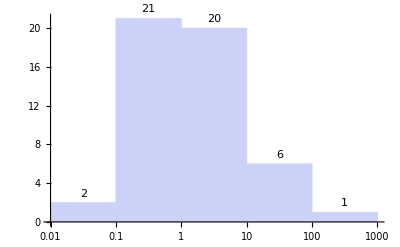

```mathematica
data=ToExpression/@Characters[Rest[StringSplit[#,"\n"]]]&/@StringSplit[Import["sudoku.txt"],"Grid"];
Monitor[Table[Timing[SudokuSolve[data[[i]]]],{i,1,50}],i];
%[[All,1]]
Histogram[%,"Log",LabelingFunction->Above]
```